# Entire lead on left side and lead of size 20 (31-50)on diagonally opposite side of right end.

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```

```mathematica
leads[10]
```

{{{0.-0.848911 ⅈ,-0.499585+0. ⅈ,0.+0.170328 ⅈ,-0.00145614+0. ⅈ,0.+0.0215636 ⅈ,0.00305462+0. ⅈ,0.+0.0108578 ⅈ,-0.00416569+0. ⅈ,0.-0.000257949 ⅈ,0.00451733+0. ⅈ},8,{0.00451733+0. ⅈ,0.-0.000257949 ⅈ,-0.00416569+0. ⅈ,0.+0.0108578 ⅈ,0.00305462+0. ⅈ,0.+0.0215636 ⅈ,-0.00145614+0. ⅈ,0.+0.170328 ⅈ,-0.499585+0. ⅈ,0.-0.848911 ⅈ}},248,{{0.497586-0.230577 ⅈ,0.128014-0.288378 ⅈ,6,-0.0166891+0.015773 ⅈ,-0.0119669+0.0352477 ⅈ},{1},6,{1},{1}}}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
Clear[dist,list]
```

```mathematica
(*FOR DIAGONAL APP
list[upleft_,downleft_,upright_,downright_]:=Module[{},Join[Transpose[Join[{Range[1,25]},{RandomSample[Join[Table[RandomInteger[{1,12}],upleft],Table[RandomInteger[{13,25}],downleft],Table[RandomInteger[{26,50}],5]]]}]],Transpose[Join[{Range[26,50]},{RandomSample[Join[Table[RandomInteger[{1,12}],upright],Table[RandomInteger[{13,25}],downright],Table[RandomInteger[{26,50}],5]]]}]]]]*)
```

```mathematica
(*dist[diagonal_]:=dist[diagonal]=Table[Module[{x=RandomInteger[{1,diagonal}]},list[x,20-x,20-(diagonal-x),diagonal-x]],5000]*)
```

```mathematica
list[up_,down_]:=Join[Transpose[Join[{Range[1,50]},{RandomSample[Join[Table[0,50-down-up],Table[RandomInteger[{1,25}],up],Table[RandomInteger[{26,50}],down]]]}]]](*,Transpose[Join[{Range[21,40]},{RandomSample[Join[Table[0,20-down],Table[RandomInteger[{21,40}],down]]]}]]]*)
```

```mathematica
dist[up_,down_]:=dist[up,down]=Table[list[up,down],5000]
```

```mathematica
TLD[t_]:=Module[{},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,31,50}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[31;;50,31;;50]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=(*Module[{sizeoflead=50},*)Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,50].SLLEAD[ω,50].T[1,50]].g[ω,0.0001,1,0]
```

```mathematica
device1[1][[1,1]]
```

0.377737-0.668031 ⅈ

```mathematica
Manipulate[Show[ListLinePlot[Table[{ω,-Im[device1[ω][[a,a]]]},{ω,Range[0,2.4,0.01]}]],ListLinePlot[Table[{ω,-Im[SLLEAD[ω,50][[a,a]]]},{ω,Range[0,2.4,0.01]}],PlotStyle->Red]],{a,Range[1,50,1]}]
```

Part::partd: Part specification device1[0.][[1,1]]
     is longer than depth of object.

Part::partd: Part specification device1[0.01][[1,1]]
     is longer than depth of object.

Part::partd: Part specification device1[0.02][[1,1]]
     is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

```mathematica
CA[ω_,ϵ1_,up_,down_,number_]:= Module[{sizeoflead=20},
recurs=Module[{J= device1[ω]},
Do[
J=Inverse[IdentityMatrix[50]-Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[up,down][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].T[1,50].J.T[1,50]].Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[up,down][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,50}];J=J];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
Mean[ParallelTable[CA[1,1,10,10,num],{num,500,1000}]]
```

10.3693

```mathematica
Table[Mean[ParallelTable[CA[1,1,x,num],{num,500}]],{x,Range[5,20,2]}]
```

{9.79884,9.71372,9.78316,9.65272,9.66763,9.68362,9.63897,9.62613}

```mathematica
Clear[tra]
```

```mathematica
transmission[up_,down_]:=Table[{ω,Mean[ParallelTable[CA[ω,1,up,down,num],{num,1500}]]},{ω,Range[0,2.49,0.01]}]
```

```mathematica
DD[YY_]:=Table[Print[x];Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_20_size_5050_epsi1_leadright/"<>ToString[YY]<>"_top_"<>ToString[x]<>"_.dat",transmission[x,YY-x]],{x,Range[5,YY,5]}]
```

```mathematica
Table[Print[YY];DD[YY],{YY,Range[10,50,10]}]
```

$Aborted

```mathematica
tr40=Table[{x,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/lead_20_size_5050_epsi1_leadright/40_top_"<>ToString[x]<>"_.dat"]},{x,Range[10,40,5]}]
```

{{10,{{0.,5.48604},{0.01,5.08265},{0.02,7.74872},{0.03,5.89978},{0.04,4.92433},{0.05,5.81069},{0.06,6.40846},{0.07,6.03098},{0.08,5.20426},{0.09,4.39999},{0.1,5.57703},{0.11,7.30335},{0.12,8.58184},{0.13,9.20958},{0.14,9.37066},{0.15,9.53466},{0.16,9.66431},{0.17,9.6163},{0.18,9.10334},{0.19,7.92386},{0.2,5.88474},{0.21,8.10997},{0.22,9.26702},{0.23,9.85618},{0.24,10.2179},{0.25,10.4161},{0.26,10.7694},{0.27,10.9161},{0.28,11.0546},{0.29,11.0094},{0.3,10.8938},{0.31,10.5954},{0.32,10.4654},{0.33,10.2787},{0.34,9.60047},{0.35,7.98021},{0.36,9.21043},{0.37,9.75721},{0.38,10.1598},{0.39,10.6085},{0.4,10.9586},{0.41,11.1501},{0.42,11.2986},{0.43,11.3466},{0.44,11.3076},{0.45,11.1804},{0.46,11.1617},{0.47,11.2418},{0.48,11.2629},{0.49,11.1878},{0.5,11.0806},{0.51,10.8595},{0.52,10.3226},{0.53,9.16905},{0.54,8.92558},{0.55,9.77814},{0.56,10.3381},{0.57,10.6827},{0.58,10.7863},{0.59,10.9621},{0.6,11.0056},{0.61,10.9941},{0.62,10.9822},{0.63,11.0885},{0.64,11.2035},{0.65,11.2914},{0.66,11.3008},{0.67,11.2859},{0.68,11.257},{0.69,11.1663},{0.7,10.9858},{0.71,10.7605},{0.72,10.642},{0.73,10.5677},{0.74,10.3115},{0.75,9.57002},{0.76,9.42564},{0.77,9.79668},{0.78,10.0777},{0.79,10.2199},{0.8,10.2505},{0.81,10.3232},{0.82,10.5688},{0.83,10.7471},{0.84,10.8118},{0.85,10.909},{0.86,10.9509},{0.87,10.9546},{0.88,10.9355},{0.89,10.8448},{0.9,10.7475},{0.91,10.6303},{0.92,10.6887},{0.93,10.7452},{0.94,10.7566},{0.95,10.6763},{0.96,10.633},{0.97,10.5036},{0.98,10.2431},{0.99,9.8287},{1.,8.09065},{1.01,8.83311},{1.02,9.27628},{1.03,9.70125},{1.04,9.94872},{1.05,10.0813},{1.06,10.1666},{1.07,10.2494},{1.08,10.2626},{1.09,10.3155},{1.1,10.301},{1.11,10.2217},{1.12,10.1531},{1.13,10.2039},{1.14,10.3126},{1.15,10.3722},{1.16,10.3826},{1.17,10.3904},{1.18,10.3853},{1.19,10.346},{1.2,10.3035},{1.21,10.2061},{1.22,10.0637},{1.23,9.82843},{1.24,9.67884},{1.25,9.60917},{1.26,9.36778},{1.27,8.33482},{1.28,8.86079},{1.29,9.11666},{1.3,9.24824},{1.31,9.35573},{1.32,9.4114},{1.33,9.44142},{1.34,9.41706},{1.35,9.35248},{1.36,9.51954},{1.37,9.66856},{1.38,9.75699},{1.39,9.77208},{1.4,9.80029},{1.41,9.80038},{1.42,9.79959},{1.43,9.79253},{1.44,9.7522},{1.45,9.65836},{1.46,9.49069},{1.47,9.42072},{1.48,9.50147},{1.49,9.54719},{1.5,9.52611},{1.51,9.4984},{1.52,9.40232},{1.53,9.28179},{1.54,9.0961},{1.55,8.59278},{1.56,7.93255},{1.57,8.10923},{1.58,8.20677},{1.59,8.36874},{1.6,8.63273},{1.61,8.8072},{1.62,8.90679},{1.63,8.95196},{1.64,8.9972},{1.65,9.03456},{1.66,9.04577},{1.67,9.0297},{1.68,9.04556},{1.69,8.98046},{1.7,8.8405},{1.71,8.81216},{1.72,8.89117},{1.73,8.97517},{1.74,9.00253},{1.75,9.01253},{1.76,9.0015},{1.77,8.99204},{1.78,8.95357},{1.79,8.89317},{1.8,8.82906},{1.81,8.68137},{1.82,8.43504},{1.83,8.19556},{1.84,8.01531},{1.85,7.25104},{1.86,7.56422},{1.87,7.78305},{1.88,7.90265},{1.89,7.99005},{1.9,8.06974},{1.91,8.09067},{1.92,8.12658},{1.93,8.11126},{1.94,8.04477},{1.95,7.99202},{1.96,8.05566},{1.97,8.18087},{1.98,8.24577},{1.99,8.28715},{2.,8.3021},{2.01,8.2951},{2.02,8.30174},{2.03,8.27867},{2.04,8.24035},{2.05,8.21895},{2.06,8.11099},{2.07,7.94928},{2.08,7.88407},{2.09,7.94089},{2.1,7.98585},{2.11,7.96009},{2.12,7.86526},{2.13,7.74219},{2.14,7.4778},{2.15,6.52975},{2.16,6.80028},{2.17,6.93596},{2.18,6.93788},{2.19,6.95279},{2.2,6.9844},{2.21,7.15362},{2.22,7.29106},{2.23,7.38812},{2.24,7.43158},{2.25,7.45608},{2.26,7.46034},{2.27,7.47863},{2.28,7.44843},{2.29,7.44102},{2.3,7.41078},{2.31,7.31057},{2.32,7.2093},{2.33,7.24303},{2.34,7.32606},{2.35,7.36225},{2.36,7.38145},{2.37,7.36635},{2.38,7.3396},{2.39,7.30501},{2.4,7.23728},{2.41,7.14764},{2.42,7.01117},{2.43,6.70085},{2.44,6.22034},{2.45,5.65343},{2.46,6.05897},{2.47,6.25838},{2.48,6.38923},{2.49,6.41946}}},{15,{{0.,5.4252},{0.01,5.1372},{0.02,7.40435},{0.03,5.93613},{0.04,5.27709},{0.05,6.3122},{0.06,6.85882},{0.07,6.73196},{0.08,5.74151},{0.09,4.64767},{0.1,6.38466},{0.11,8.03555},{0.12,9.24337},{0.13,9.70349},{0.14,9.93509},{0.15,10.0696},{0.16,10.1491},{0.17,10.042},{0.18,9.62201},{0.19,8.46226},{0.2,6.56991},{0.21,8.77638},{0.22,9.91537},{0.23,10.4013},{0.24,10.7214},{0.25,10.9122},{0.26,11.1421},{0.27,11.3609},{0.28,11.4659},{0.29,11.4571},{0.3,11.2956},{0.31,11.0085},{0.32,10.875},{0.33,10.6528},{0.34,9.98113},{0.35,8.54787},{0.36,9.70621},{0.37,10.2751},{0.38,10.6421},{0.39,11.013},{0.4,11.3739},{0.41,11.5099},{0.42,11.6252},{0.43,11.6801},{0.44,11.6675},{0.45,11.5165},{0.46,11.4219},{0.47,11.5327},{0.48,11.5436},{0.49,11.5197},{0.5,11.3979},{0.51,11.1713},{0.52,10.6992},{0.53,9.59681},{0.54,9.33541},{0.55,10.2521},{0.56,10.6287},{0.57,10.9347},{0.58,11.1424},{0.59,11.2438},{0.6,11.3388},{0.61,11.3376},{0.62,11.2537},{0.63,11.3395},{0.64,11.4772},{0.65,11.5556},{0.66,11.5484},{0.67,11.5577},{0.68,11.549},{0.69,11.4433},{0.7,11.2844},{0.71,11.0469},{0.72,10.9523},{0.73,10.8644},{0.74,10.5997},{0.75,9.92724},{0.76,9.77107},{0.77,10.1402},{0.78,10.414},{0.79,10.5429},{0.8,10.5619},{0.81,10.6087},{0.82,10.8379},{0.83,11.0044},{0.84,11.0838},{0.85,11.1396},{0.86,11.19},{0.87,11.1712},{0.88,11.169},{0.89,11.1335},{0.9,10.9882},{0.91,10.863},{0.92,10.9315},{0.93,10.9779},{0.94,10.9573},{0.95,10.9341},{0.96,10.8712},{0.97,10.7347},{0.98,10.5278},{0.99,10.1714},{1.,8.48158},{1.01,9.11951},{1.02,9.54556},{1.03,9.97649},{1.04,10.2103},{1.05,10.2917},{1.06,10.4173},{1.07,10.4764},{1.08,10.5013},{1.09,10.5229},{1.1,10.5167},{1.11,10.4653},{1.12,10.3657},{1.13,10.399},{1.14,10.5048},{1.15,10.5578},{1.16,10.5831},{1.17,10.5897},{1.18,10.5764},{1.19,10.5426},{1.2,10.4992},{1.21,10.4323},{1.22,10.2761},{1.23,10.0414},{1.24,9.90986},{1.25,9.84658},{1.26,9.62231},{1.27,8.63745},{1.28,9.13298},{1.29,9.36875},{1.3,9.51098},{1.31,9.55336},{1.32,9.64695},{1.33,9.66434},{1.34,9.61764},{1.35,9.61013},{1.36,9.74067},{1.37,9.84825},{1.38,9.91227},{1.39,9.94275},{1.4,9.96651},{1.41,9.97616},{1.42,9.97826},{1.43,9.95327},{1.44,9.92249},{1.45,9.85587},{1.46,9.68841},{1.47,9.6167},{1.48,9.68779},{1.49,9.72376},{1.5,9.72198},{1.51,9.68218},{1.52,9.59439},{1.53,9.50205},{1.54,9.29127},{1.55,8.82357},{1.56,8.20115},{1.57,8.35966},{1.58,8.45524},{1.59,8.58833},{1.6,8.8403},{1.61,8.99481},{1.62,9.06274},{1.63,9.12913},{1.64,9.14999},{1.65,9.18759},{1.66,9.1984},{1.67,9.19819},{1.68,9.19564},{1.69,9.13262},{1.7,9.00344},{1.71,8.96008},{1.72,9.04963},{1.73,9.12606},{1.74,9.16228},{1.75,9.16672},{1.76,9.1586},{1.77,9.14653},{1.78,9.11177},{1.79,9.05281},{1.8,8.99257},{1.81,8.86605},{1.82,8.6496},{1.83,8.39032},{1.84,8.21888},{1.85,7.51815},{1.86,7.75976},{1.87,7.99588},{1.88,8.09082},{1.89,8.16736},{1.9,8.2373},{1.91,8.25797},{1.92,8.28474},{1.93,8.29581},{1.94,8.22779},{1.95,8.14511},{1.96,8.2002},{1.97,8.32735},{1.98,8.38419},{1.99,8.41738},{2.,8.43134},{2.01,8.4421},{2.02,8.43101},{2.03,8.42733},{2.04,8.39178},{2.05,8.36147},{2.06,8.2664},{2.07,8.12238},{2.08,8.0339},{2.09,8.10321},{2.1,8.11868},{2.11,8.09207},{2.12,8.03932},{2.13,7.90141},{2.14,7.65944},{2.15,6.72081},{2.16,6.99843},{2.17,7.13339},{2.18,7.13563},{2.19,7.1473},{2.2,7.14384},{2.21,7.30681},{2.22,7.44029},{2.23,7.51913},{2.24,7.56203},{2.25,7.58036},{2.26,7.59589},{2.27,7.60955},{2.28,7.59007},{2.29,7.57871},{2.3,7.55148},{2.31,7.45712},{2.32,7.35301},{2.33,7.37542},{2.34,7.46592},{2.35,7.49626},{2.36,7.50425},{2.37,7.48794},{2.38,7.45855},{2.39,7.43597},{2.4,7.36898},{2.41,7.28273},{2.42,7.15014},{2.43,6.86168},{2.44,6.35881},{2.45,5.82986},{2.46,6.18413},{2.47,6.41055},{2.48,6.51593},{2.49,6.56874}}},{20,{{0.,5.64071},{0.01,4.89878},{0.02,7.06641},{0.03,5.58277},{0.04,6.07719},{0.05,7.24712},{0.06,7.81014},{0.07,7.43166},{0.08,6.57829},{0.09,4.93028},{0.1,7.22508},{0.11,8.93605},{0.12,9.98546},{0.13,10.4287},{0.14,10.606},{0.15,10.5853},{0.16,10.6905},{0.17,10.6477},{0.18,10.2879},{0.19,9.1627},{0.2,7.23407},{0.21,9.49037},{0.22,10.4619},{0.23,11.0483},{0.24,11.1851},{0.25,11.4049},{0.26,11.6093},{0.27,11.7692},{0.28,11.8204},{0.29,11.8439},{0.3,11.6673},{0.31,11.4087},{0.32,11.2255},{0.33,11.0935},{0.34,10.4789},{0.35,9.2152},{0.36,10.2522},{0.37,10.7574},{0.38,11.1028},{0.39,11.4455},{0.4,11.7332},{0.41,11.8895},{0.42,11.9515},{0.43,12.0456},{0.44,12.0111},{0.45,11.835},{0.46,11.8206},{0.47,11.8721},{0.48,11.9112},{0.49,11.8649},{0.5,11.7697},{0.51,11.538},{0.52,11.1168},{0.53,10.0423},{0.54,9.77257},{0.55,10.5872},{0.56,11.02},{0.57,11.3154},{0.58,11.4652},{0.59,11.5843},{0.6,11.632},{0.61,11.5993},{0.62,11.5529},{0.63,11.6452},{0.64,11.7559},{0.65,11.8044},{0.66,11.8597},{0.67,11.8465},{0.68,11.8079},{0.69,11.7426},{0.7,11.574},{0.71,11.3645},{0.72,11.2532},{0.73,11.1999},{0.74,10.9582},{0.75,10.3351},{0.76,10.0878},{0.77,10.4775},{0.78,10.7381},{0.79,10.8297},{0.8,10.8529},{0.81,10.9082},{0.82,11.1253},{0.83,11.2599},{0.84,11.3434},{0.85,11.3851},{0.86,11.413},{0.87,11.4074},{0.88,11.4089},{0.89,11.3692},{0.9,11.2317},{0.91,11.1205},{0.92,11.1725},{0.93,11.2259},{0.94,11.2309},{0.95,11.2048},{0.96,11.1266},{0.97,10.9928},{0.98,10.8089},{0.99,10.4539},{1.,8.85146},{1.01,9.52145},{1.02,9.91855},{1.03,10.2473},{1.04,10.4613},{1.05,10.5707},{1.06,10.648},{1.07,10.7304},{1.08,10.742},{1.09,10.7504},{1.1,10.7465},{1.11,10.6961},{1.12,10.5923},{1.13,10.6185},{1.14,10.7157},{1.15,10.7917},{1.16,10.8005},{1.17,10.8012},{1.18,10.7827},{1.19,10.7528},{1.2,10.7129},{1.21,10.6402},{1.22,10.5223},{1.23,10.2949},{1.24,10.1555},{1.25,10.0871},{1.26,9.88111},{1.27,8.90938},{1.28,9.3722},{1.29,9.61802},{1.3,9.74665},{1.31,9.82456},{1.32,9.88755},{1.33,9.88597},{1.34,9.84299},{1.35,9.81656},{1.36,9.94371},{1.37,10.0474},{1.38,10.1264},{1.39,10.1375},{1.4,10.16},{1.41,10.163},{1.42,10.168},{1.43,10.1443},{1.44,10.125},{1.45,10.0569},{1.46,9.89643},{1.47,9.80412},{1.48,9.87592},{1.49,9.91798},{1.5,9.91598},{1.51,9.87591},{1.52,9.81568},{1.53,9.69592},{1.54,9.5091},{1.55,9.06342},{1.56,8.50467},{1.57,8.62574},{1.58,8.69728},{1.59,8.82219},{1.6,9.03927},{1.61,9.17512},{1.62,9.26762},{1.63,9.31348},{1.64,9.33449},{1.65,9.37082},{1.66,9.37436},{1.67,9.37439},{1.68,9.38013},{1.69,9.30661},{1.7,9.20083},{1.71,9.1416},{1.72,9.23588},{1.73,9.2975},{1.74,9.33063},{1.75,9.33329},{1.76,9.3227},{1.77,9.30585},{1.78,9.28206},{1.79,9.2233},{1.8,9.15821},{1.81,9.04287},{1.82,8.82433},{1.83,8.59879},{1.84,8.43121},{1.85,7.72428},{1.86,7.96633},{1.87,8.17019},{1.88,8.26179},{1.89,8.33664},{1.9,8.40912},{1.91,8.42669},{1.92,8.43973},{1.93,8.44334},{1.94,8.3931},{1.95,8.33721},{1.96,8.378},{1.97,8.47746},{1.98,8.53749},{1.99,8.58182},{2.,8.58841},{2.01,8.58339},{2.02,8.58965},{2.03,8.576},{2.04,8.54712},{2.05,8.51587},{2.06,8.43211},{2.07,8.28477},{2.08,8.22495},{2.09,8.26828},{2.1,8.30018},{2.11,8.27326},{2.12,8.19576},{2.13,8.06958},{2.14,7.83742},{2.15,6.93405},{2.16,7.18051},{2.17,7.29709},{2.18,7.33425},{2.19,7.3412},{2.2,7.33635},{2.21,7.4876},{2.22,7.59721},{2.23,7.67428},{2.24,7.70717},{2.25,7.72866},{2.26,7.72573},{2.27,7.74521},{2.28,7.73642},{2.29,7.71288},{2.3,7.69234},{2.31,7.59766},{2.32,7.50745},{2.33,7.52654},{2.34,7.61197},{2.35,7.64239},{2.36,7.63732},{2.37,7.633},{2.38,7.61387},{2.39,7.56971},{2.4,7.51373},{2.41,7.44188},{2.42,7.30415},{2.43,7.03618},{2.44,6.56269},{2.45,6.01915},{2.46,6.3894},{2.47,6.56442},{2.48,6.67894},{2.49,6.70912}}},{25,{{0.,5.78846},{0.01,5.25853},{0.02,6.46203},{0.03,6.23157},{0.04,7.26401},{0.05,8.40139},{0.06,8.83451},{0.07,8.51106},{0.08,7.63835},{0.09,5.64738},{0.1,8.50877},{0.11,9.94839},{0.12,10.768},{0.13,11.2482},{0.14,11.2858},{0.15,11.3091},{0.16,11.3197},{0.17,11.3486},{0.18,10.9403},{0.19,10.0256},{0.2,8.31445},{0.21,10.3814},{0.22,11.2961},{0.23,11.7212},{0.24,11.8862},{0.25,11.979},{0.26,12.1693},{0.27,12.2906},{0.28,12.3722},{0.29,12.3786},{0.3,12.2134},{0.31,11.9622},{0.32,11.819},{0.33,11.6444},{0.34,11.1149},{0.35,9.92268},{0.36,10.9509},{0.37,11.3353},{0.38,11.6278},{0.39,11.9324},{0.4,12.1792},{0.41,12.3087},{0.42,12.4068},{0.43,12.4287},{0.44,12.4196},{0.45,12.2702},{0.46,12.2314},{0.47,12.2755},{0.48,12.3077},{0.49,12.2667},{0.5,12.1739},{0.51,11.9915},{0.52,11.6089},{0.53,10.6579},{0.54,10.4976},{0.55,11.1441},{0.56,11.5297},{0.57,11.7548},{0.58,11.8939},{0.59,11.9985},{0.6,12.008},{0.61,11.9798},{0.62,11.935},{0.63,11.9966},{0.64,12.1167},{0.65,12.1578},{0.66,12.1872},{0.67,12.1631},{0.68,12.1571},{0.69,12.0789},{0.7,11.9182},{0.71,11.6921},{0.72,11.6163},{0.73,11.5583},{0.74,11.3612},{0.75,10.7662},{0.76,10.5967},{0.77,10.9037},{0.78,11.1125},{0.79,11.2132},{0.8,11.2224},{0.81,11.2644},{0.82,11.4231},{0.83,11.5782},{0.84,11.6224},{0.85,11.6844},{0.86,11.7161},{0.87,11.7074},{0.88,11.7028},{0.89,11.658},{0.9,11.5372},{0.91,11.4311},{0.92,11.4563},{0.93,11.5103},{0.94,11.5188},{0.95,11.4941},{0.96,11.4185},{0.97,11.3111},{0.98,11.1386},{0.99,10.8228},{1.,9.33856},{1.01,9.92772},{1.02,10.2743},{1.03,10.5883},{1.04,10.7597},{1.05,10.8612},{1.06,10.9394},{1.07,10.9935},{1.08,11.0126},{1.09,11.0247},{1.1,11.0198},{1.11,10.9505},{1.12,10.8716},{1.13,10.8792},{1.14,10.9852},{1.15,11.0153},{1.16,11.0467},{1.17,11.0385},{1.18,11.0334},{1.19,10.9969},{1.2,10.9632},{1.21,10.91},{1.22,10.7859},{1.23,10.5764},{1.24,10.4534},{1.25,10.3947},{1.26,10.1941},{1.27,9.30497},{1.28,9.68247},{1.29,9.92337},{1.3,10.0372},{1.31,10.0638},{1.32,10.1304},{1.33,10.1428},{1.34,10.0916},{1.35,10.0618},{1.36,10.1658},{1.37,10.2654},{1.38,10.3194},{1.39,10.3436},{1.4,10.3594},{1.41,10.3748},{1.42,10.3602},{1.43,10.3554},{1.44,10.3276},{1.45,10.2682},{1.46,10.119},{1.47,10.0434},{1.48,10.1042},{1.49,10.1362},{1.5,10.1305},{1.51,10.0927},{1.52,10.0322},{1.53,9.93386},{1.54,9.75241},{1.55,9.32812},{1.56,8.78187},{1.57,8.95044},{1.58,8.9846},{1.59,9.10264},{1.6,9.28513},{1.61,9.4091},{1.62,9.47435},{1.63,9.52539},{1.64,9.52346},{1.65,9.5731},{1.66,9.57748},{1.67,9.55252},{1.68,9.57215},{1.69,9.52363},{1.7,9.39714},{1.71,9.33143},{1.72,9.43775},{1.73,9.49637},{1.74,9.51864},{1.75,9.5093},{1.76,9.50548},{1.77,9.48553},{1.78,9.46688},{1.79,9.42547},{1.8,9.36766},{1.81,9.27501},{1.82,9.06823},{1.83,8.85086},{1.84,8.69788},{1.85,8.01778},{1.86,8.2396},{1.87,8.41318},{1.88,8.50179},{1.89,8.5479},{1.9,8.61535},{1.91,8.63613},{1.92,8.65769},{1.93,8.64936},{1.94,8.59354},{1.95,8.51752},{1.96,8.56867},{1.97,8.66775},{1.98,8.72216},{1.99,8.73291},{2.,8.75194},{2.01,8.74811},{2.02,8.75694},{2.03,8.74311},{2.04,8.71046},{2.05,8.68517},{2.06,8.61101},{2.07,8.47537},{2.08,8.41479},{2.09,8.45528},{2.1,8.47897},{2.11,8.44283},{2.12,8.38995},{2.13,8.26575},{2.14,8.05298},{2.15,7.17949},{2.16,7.41011},{2.17,7.51131},{2.18,7.55821},{2.19,7.54332},{2.2,7.54301},{2.21,7.67527},{2.22,7.78298},{2.23,7.84114},{2.24,7.8834},{2.25,7.88261},{2.26,7.89187},{2.27,7.91054},{2.28,7.88546},{2.29,7.8818},{2.3,7.84479},{2.31,7.76918},{2.32,7.67663},{2.33,7.70466},{2.34,7.76491},{2.35,7.80031},{2.36,7.79944},{2.37,7.7909},{2.38,7.77383},{2.39,7.73466},{2.4,7.67988},{2.41,7.60624},{2.42,7.49753},{2.43,7.24174},{2.44,6.81313},{2.45,6.2617},{2.46,6.57131},{2.47,6.75738},{2.48,6.84702},{2.49,6.88808}}},{30,{{0.,6.46845},{0.01,5.5001},{0.02,5.73633},{0.03,7.04584},{0.04,8.74609},{0.05,9.87281},{0.06,10.0598},{0.07,9.69958},{0.08,9.01934},{0.09,6.796},{0.1,9.89125},{0.11,11.015},{0.12,11.7225},{0.13,12.1012},{0.14,12.1002},{0.15,12.1044},{0.16,12.1145},{0.17,12.0887},{0.18,11.7818},{0.19,10.8723},{0.2,9.32592},{0.21,11.3158},{0.22,12.0338},{0.23,12.4262},{0.24,12.5752},{0.25,12.5999},{0.26,12.7522},{0.27,12.9},{0.28,12.9246},{0.29,12.9261},{0.3,12.7763},{0.31,12.5566},{0.32,12.4115},{0.33,12.2662},{0.34,11.8166},{0.35,10.7637},{0.36,11.7143},{0.37,12.0432},{0.38,12.224},{0.39,12.4803},{0.4,12.6812},{0.41,12.7964},{0.42,12.8629},{0.43,12.895},{0.44,12.8564},{0.45,12.701},{0.46,12.6824},{0.47,12.7374},{0.48,12.7481},{0.49,12.7164},{0.5,12.6266},{0.51,12.4483},{0.52,12.1346},{0.53,11.272},{0.54,11.0694},{0.55,11.6707},{0.56,12.0066},{0.57,12.1922},{0.58,12.2861},{0.59,12.3903},{0.6,12.4282},{0.61,12.3505},{0.62,12.3131},{0.63,12.3808},{0.64,12.4401},{0.65,12.5137},{0.66,12.5423},{0.67,12.5126},{0.68,12.4951},{0.69,12.4259},{0.7,12.264},{0.71,12.102},{0.72,12.0394},{0.73,11.9851},{0.74,11.7741},{0.75,11.2379},{0.76,11.0545},{0.77,11.3342},{0.78,11.529},{0.79,11.5984},{0.8,11.5937},{0.81,11.6367},{0.82,11.7823},{0.83,11.8828},{0.84,11.9282},{0.85,11.9689},{0.86,11.9955},{0.87,11.9954},{0.88,12.0066},{0.89,11.9491},{0.9,11.8309},{0.91,11.7311},{0.92,11.7726},{0.93,11.8194},{0.94,11.8163},{0.95,11.806},{0.96,11.7476},{0.97,11.6324},{0.98,11.4683},{0.99,11.1947},{1.,9.83412},{1.01,10.3459},{1.02,10.6453},{1.03,10.9184},{1.04,11.083},{1.05,11.1565},{1.06,11.2107},{1.07,11.2553},{1.08,11.2673},{1.09,11.2944},{1.1,11.286},{1.11,11.23},{1.12,11.1323},{1.13,11.1467},{1.14,11.2197},{1.15,11.2857},{1.16,11.2926},{1.17,11.2989},{1.18,11.2725},{1.19,11.2683},{1.2,11.2286},{1.21,11.167},{1.22,11.0675},{1.23,10.867},{1.24,10.7366},{1.25,10.699},{1.26,10.5039},{1.27,9.65791},{1.28,10.0134},{1.29,10.2035},{1.3,10.2968},{1.31,10.3597},{1.32,10.4151},{1.33,10.4214},{1.34,10.3694},{1.35,10.3482},{1.36,10.4342},{1.37,10.4977},{1.38,10.5468},{1.39,10.5781},{1.4,10.5941},{1.41,10.5923},{1.42,10.5848},{1.43,10.569},{1.44,10.5617},{1.45,10.5077},{1.46,10.3518},{1.47,10.3017},{1.48,10.3562},{1.49,10.3938},{1.5,10.3776},{1.51,10.3408},{1.52,10.2706},{1.53,10.1802},{1.54,10.0152},{1.55,9.62192},{1.56,9.08682},{1.57,9.22786},{1.58,9.28368},{1.59,9.36564},{1.6,9.52657},{1.61,9.62178},{1.62,9.70006},{1.63,9.72756},{1.64,9.74124},{1.65,9.76907},{1.66,9.769},{1.67,9.75967},{1.68,9.76515},{1.69,9.73517},{1.7,9.61763},{1.71,9.56476},{1.72,9.64826},{1.73,9.68807},{1.74,9.71358},{1.75,9.71732},{1.76,9.70841},{1.77,9.6844},{1.78,9.65937},{1.79,9.63445},{1.8,9.57542},{1.81,9.48805},{1.82,9.3113},{1.83,9.10864},{1.84,8.95453},{1.85,8.31824},{1.86,8.48959},{1.87,8.64042},{1.88,8.70904},{1.89,8.75984},{1.9,8.82424},{1.91,8.83453},{1.92,8.83765},{1.93,8.85676},{1.94,8.79809},{1.95,8.73182},{1.96,8.78142},{1.97,8.85953},{1.98,8.9009},{1.99,8.92734},{2.,8.93768},{2.01,8.93126},{2.02,8.92308},{2.03,8.91281},{2.04,8.88482},{2.05,8.86755},{2.06,8.81413},{2.07,8.67978},{2.08,8.61993},{2.09,8.65952},{2.1,8.67813},{2.11,8.64732},{2.12,8.57774},{2.13,8.47939},{2.14,8.25851},{2.15,7.44467},{2.16,7.62328},{2.17,7.72757},{2.18,7.78759},{2.19,7.7697},{2.2,7.76535},{2.21,7.88137},{2.22,7.95902},{2.23,8.01128},{2.24,8.03671},{2.25,8.04948},{2.26,8.05809},{2.27,8.06922},{2.28,8.05775},{2.29,8.04649},{2.3,8.02807},{2.31,7.95315},{2.32,7.86801},{2.33,7.88009},{2.34,7.94623},{2.35,7.96713},{2.36,7.95946},{2.37,7.9549},{2.38,7.93021},{2.39,7.89301},{2.4,7.85266},{2.41,7.78597},{2.42,7.67843},{2.43,7.44832},{2.44,7.03191},{2.45,6.51528},{2.46,6.79464},{2.47,6.94746},{2.48,7.02582},{2.49,7.0498}}},{35,{{0.,7.40931},{0.01,6.62136},{0.02,5.54237},{0.03,8.91836},{0.04,10.5874},{0.05,11.2999},{0.06,11.4537},{0.07,11.144},{0.08,10.5706},{0.09,8.43061},{0.1,11.3623},{0.11,12.2849},{0.12,12.8171},{0.13,13.0713},{0.14,12.9941},{0.15,12.9871},{0.16,13.0008},{0.17,12.9878},{0.18,12.7256},{0.19,11.9716},{0.2,10.7892},{0.21,12.2517},{0.22,12.9012},{0.23,13.165},{0.24,13.2211},{0.25,13.2393},{0.26,13.3738},{0.27,13.4603},{0.28,13.5383},{0.29,13.5325},{0.3,13.3956},{0.31,13.1738},{0.32,13.0737},{0.33,12.9557},{0.34,12.5485},{0.35,11.7027},{0.36,12.4116},{0.37,12.6996},{0.38,12.8012},{0.39,13.0073},{0.4,13.1878},{0.41,13.2715},{0.42,13.3417},{0.43,13.3406},{0.44,13.3357},{0.45,13.1625},{0.46,13.1548},{0.47,13.2079},{0.48,13.2362},{0.49,13.2172},{0.5,13.1144},{0.51,12.9986},{0.52,12.7376},{0.53,11.9883},{0.54,11.7108},{0.55,12.2503},{0.56,12.4618},{0.57,12.6311},{0.58,12.7234},{0.59,12.8073},{0.6,12.8118},{0.61,12.7681},{0.62,12.7104},{0.63,12.7691},{0.64,12.8225},{0.65,12.8573},{0.66,12.887},{0.67,12.8714},{0.68,12.8418},{0.69,12.8295},{0.7,12.6776},{0.71,12.5129},{0.72,12.4377},{0.73,12.4071},{0.74,12.2336},{0.75,11.7794},{0.76,11.5402},{0.77,11.7711},{0.78,11.962},{0.79,12.0146},{0.8,11.9905},{0.81,12.0168},{0.82,12.1334},{0.83,12.2098},{0.84,12.2567},{0.85,12.3034},{0.86,12.3121},{0.87,12.2989},{0.88,12.3105},{0.89,12.2701},{0.9,12.162},{0.91,12.0668},{0.92,12.101},{0.93,12.1451},{0.94,12.1423},{0.95,12.1251},{0.96,12.0808},{0.97,11.9758},{0.98,11.8228},{0.99,11.5769},{1.,10.3447},{1.01,10.8076},{1.02,11.0612},{1.03,11.2789},{1.04,11.3996},{1.05,11.4528},{1.06,11.511},{1.07,11.5515},{1.08,11.555},{1.09,11.5652},{1.1,11.5806},{1.11,11.5152},{1.12,11.4244},{1.13,11.44},{1.14,11.5049},{1.15,11.538},{1.16,11.553},{1.17,11.5577},{1.18,11.5365},{1.19,11.5176},{1.2,11.4953},{1.21,11.4469},{1.22,11.3498},{1.23,11.1831},{1.24,11.0845},{1.25,11.0351},{1.26,10.8511},{1.27,10.0617},{1.28,10.3579},{1.29,10.5054},{1.3,10.607},{1.31,10.6205},{1.32,10.6842},{1.33,10.6846},{1.34,10.631},{1.35,10.5957},{1.36,10.6841},{1.37,10.7538},{1.38,10.7858},{1.39,10.8183},{1.4,10.8208},{1.41,10.8235},{1.42,10.8053},{1.43,10.7909},{1.44,10.7916},{1.45,10.7406},{1.46,10.6235},{1.47,10.5678},{1.48,10.6168},{1.49,10.6244},{1.5,10.6183},{1.51,10.5826},{1.52,10.5253},{1.53,10.4334},{1.54,10.281},{1.55,9.93445},{1.56,9.42268},{1.57,9.56959},{1.58,9.58378},{1.59,9.64903},{1.6,9.77948},{1.61,9.86519},{1.62,9.91487},{1.63,9.94675},{1.64,9.95981},{1.65,9.9792},{1.66,9.98325},{1.67,9.9769},{1.68,9.98041},{1.69,9.94032},{1.7,9.85583},{1.71,9.80822},{1.72,9.86908},{1.73,9.9061},{1.74,9.92805},{1.75,9.92633},{1.76,9.91618},{1.77,9.89671},{1.78,9.87545},{1.79,9.83767},{1.8,9.79902},{1.81,9.72884},{1.82,9.57351},{1.83,9.39291},{1.84,9.22773},{1.85,8.64568},{1.86,8.76456},{1.87,8.89099},{1.88,8.93478},{1.89,8.97991},{1.9,9.03215},{1.91,9.04354},{1.92,9.05086},{1.93,9.06011},{1.94,9.00987},{1.95,8.95778},{1.96,8.99128},{1.97,9.05962},{1.98,9.10044},{1.99,9.10889},{2.,9.10957},{2.01,9.1178},{2.02,9.10186},{2.03,9.10491},{2.04,9.08797},{2.05,9.07515},{2.06,9.0138},{2.07,8.90262},{2.08,8.84726},{2.09,8.88117},{2.1,8.88894},{2.11,8.85424},{2.12,8.79052},{2.13,8.69829},{2.14,8.50264},{2.15,7.72503},{2.16,7.87731},{2.17,7.98634},{2.18,8.01538},{2.19,7.98679},{2.2,7.99394},{2.21,8.08256},{2.22,8.15048},{2.23,8.2011},{2.24,8.21923},{2.25,8.2321},{2.26,8.23433},{2.27,8.23952},{2.28,8.22181},{2.29,8.21616},{2.3,8.1957},{2.31,8.13412},{2.32,8.06681},{2.33,8.07763},{2.34,8.13174},{2.35,8.14573},{2.36,8.14286},{2.37,8.12995},{2.38,8.11436},{2.39,8.07475},{2.4,8.03171},{2.41,7.9762},{2.42,7.88522},{2.43,7.68725},{2.44,7.30678},{2.45,6.79573},{2.46,7.02979},{2.47,7.15303},{2.48,7.21879},{2.49,7.24544}}},{40,{{0.,9.08631},{0.01,9.31795},{0.02,7.95141},{0.03,12.0393},{0.04,12.9017},{0.05,13.2122},{0.06,13.2606},{0.07,13.0466},{0.08,12.5409},{0.09,11.1797},{0.1,13.1901},{0.11,13.7711},{0.12,14.0323},{0.13,14.1649},{0.14,14.0851},{0.15,14.0264},{0.16,14.0343},{0.17,14.0094},{0.18,13.8907},{0.19,13.3104},{0.2,12.4447},{0.21,13.4691},{0.22,13.875},{0.23,14.0545},{0.24,14.0434},{0.25,14.0254},{0.26,14.0921},{0.27,14.1527},{0.28,14.1978},{0.29,14.2016},{0.3,14.0879},{0.31,13.9145},{0.32,13.854},{0.33,13.7617},{0.34,13.4727},{0.35,12.7685},{0.36,13.3088},{0.37,13.4521},{0.38,13.526},{0.39,13.6523},{0.4,13.7597},{0.41,13.8167},{0.42,13.8615},{0.43,13.8899},{0.44,13.8772},{0.45,13.7157},{0.46,13.7008},{0.47,13.7518},{0.48,13.765},{0.49,13.7449},{0.5,13.694},{0.51,13.5913},{0.52,13.3591},{0.53,12.7528},{0.54,12.4756},{0.55,12.8545},{0.56,13.0513},{0.57,13.1552},{0.58,13.2123},{0.59,13.2718},{0.6,13.2649},{0.61,13.2098},{0.62,13.1614},{0.63,13.2101},{0.64,13.2669},{0.65,13.3018},{0.66,13.3168},{0.67,13.31},{0.68,13.2886},{0.69,13.2558},{0.7,13.1154},{0.71,13.0175},{0.72,12.953},{0.73,12.9236},{0.74,12.7537},{0.75,12.3345},{0.76,12.1186},{0.77,12.2677},{0.78,12.4158},{0.79,12.4584},{0.8,12.4285},{0.81,12.4323},{0.82,12.5333},{0.83,12.5932},{0.84,12.6355},{0.85,12.6535},{0.86,12.6569},{0.87,12.6687},{0.88,12.6649},{0.89,12.6289},{0.9,12.5302},{0.91,12.4603},{0.92,12.4857},{0.93,12.5068},{0.94,12.5067},{0.95,12.4875},{0.96,12.4355},{0.97,12.3687},{0.98,12.2468},{0.99,12.0189},{1.,10.963},{1.01,11.3073},{1.02,11.5081},{1.03,11.6786},{1.04,11.7628},{1.05,11.8046},{1.06,11.8343},{1.07,11.8584},{1.08,11.8705},{1.09,11.8799},{1.1,11.8764},{1.11,11.8176},{1.12,11.7552},{1.13,11.7689},{1.14,11.8053},{1.15,11.8434},{1.16,11.8531},{1.17,11.8447},{1.18,11.8287},{1.19,11.815},{1.2,11.7938},{1.21,11.7667},{1.22,11.6784},{1.23,11.5517},{1.24,11.4604},{1.25,11.3913},{1.26,11.2223},{1.27,10.4865},{1.28,10.7381},{1.29,10.8785},{1.3,10.9304},{1.31,10.9478},{1.32,10.9796},{1.33,10.9975},{1.34,10.9481},{1.35,10.9132},{1.36,10.9659},{1.37,11.024},{1.38,11.0585},{1.39,11.0695},{1.4,11.0773},{1.41,11.0746},{1.42,11.0707},{1.43,11.0635},{1.44,11.0417},{1.45,11.0196},{1.46,10.921},{1.47,10.8581},{1.48,10.8986},{1.49,10.9175},{1.5,10.8914},{1.51,10.8667},{1.52,10.8155},{1.53,10.7218},{1.54,10.5881},{1.55,10.277},{1.56,9.76703},{1.57,9.91521},{1.58,9.90471},{1.59,9.96002},{1.6,10.0639},{1.61,10.1376},{1.62,10.1807},{1.63,10.1908},{1.64,10.2008},{1.65,10.2114},{1.66,10.2143},{1.67,10.2148},{1.68,10.212},{1.69,10.1929},{1.7,10.1092},{1.71,10.0715},{1.72,10.1158},{1.73,10.1467},{1.74,10.155},{1.75,10.1576},{1.76,10.1458},{1.77,10.131},{1.78,10.1142},{1.79,10.0754},{1.8,10.0446},{1.81,9.98467},{1.82,9.85419},{1.83,9.69596},{1.84,9.55239},{1.85,8.98811},{1.86,9.06756},{1.87,9.16402},{1.88,9.19185},{1.89,9.23532},{1.9,9.27357},{1.91,9.27525},{1.92,9.28186},{1.93,9.28786},{1.94,9.24712},{1.95,9.1972},{1.96,9.22801},{1.97,9.28155},{1.98,9.30754},{1.99,9.31801},{2.,9.3246},{2.01,9.32236},{2.02,9.31065},{2.03,9.30019},{2.04,9.29071},{2.05,9.27275},{2.06,9.24194},{2.07,9.15257},{2.08,9.10017},{2.09,9.12756},{2.1,9.12724},{2.11,9.08953},{2.12,9.03545},{2.13,8.94735},{2.14,8.75686},{2.15,8.01659},{2.16,8.156},{2.17,8.22045},{2.18,8.25962},{2.19,8.24557},{2.2,8.24584},{2.21,8.31766},{2.22,8.38045},{2.23,8.40184},{2.24,8.42226},{2.25,8.42037},{2.26,8.42781},{2.27,8.42071},{2.28,8.4152},{2.29,8.40453},{2.3,8.39476},{2.31,8.3459},{2.32,8.27931},{2.33,8.30132},{2.34,8.33226},{2.35,8.33205},{2.36,8.33834},{2.37,8.33366},{2.38,8.30983},{2.39,8.27736},{2.4,8.24256},{2.41,8.18932},{2.42,8.10603},{2.43,7.94468},{2.44,7.59955},{2.45,7.09552},{2.46,7.29366},{2.47,7.39365},{2.48,7.43469},{2.49,7.44134}}}}

```mathematica
Dimensions[tr40]
```

{7,2}

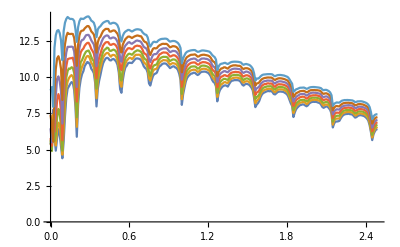

```mathematica
ListLinePlot[tr40]
```

```mathematica
CA[1,1,25,15,1]
```

9.62708

```mathematica
input= Table[ParallelTable[{ω,CA[ω,1,20,20,num]},{ω,Range[0,2.49,0.01]}],{num,50}]
```

{{{0.,9.08829},{0.01,7.17937},{0.02,5.14933},{0.03,9.30472},{0.04,9.58551},{0.05,9.36779},238,{2.44,7.01482},{2.45,6.75247},{2.46,6.85461},{2.47,6.89242},{2.48,6.96035},{2.49,6.99809}},48,{1}}
 |  |  |  |

```mathematica
Dimensions[tr40[[1,2]]]
```

{250,2}

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{tr50[[con,1]],Module[{B1=Transpose[{m5[[1;;250]][[;;,1]],(m5[[1;;250,2]]-tr40[[con,2]][[1;;250,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{con,7}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

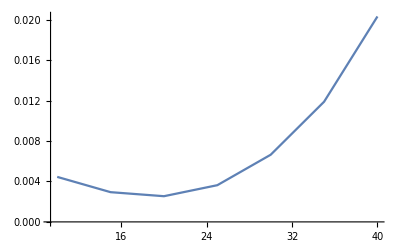

```mathematica
ListLinePlot[misfit[2,0.5,1][[1]]]
```

```mathematica
Table[Abs[misfit[2.49,0.5,num][[2]][[1]]-20]/20,{num,50}]//Mean
```

7/30

```mathematica
N[31/200]
```

0.155

```mathematica
N[21/125]
```

0.168

```mathematica
N[1/12]
```

0.0833333

```mathematica
N[23/125]
```

0.184

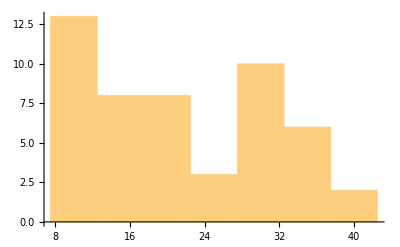

```mathematica
Histogram[%68]
```

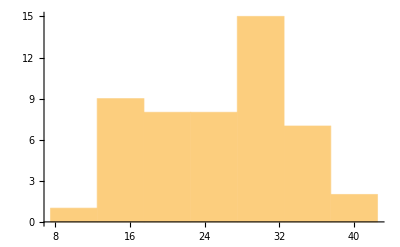

```mathematica
Histogram[{15,35,25,35,35,15,30,20,30,25,15,15,20,25,20,35,10,20,35,30,30,20,25,15,20,15,30,25,40,15,25,30,35,20,30,25,30,15,20,15,30,25,40,30,30,30,30,30,35,30}]
```